```mathematica
(*Function that computes the values of the endpoints in the smooth regime*)
getstdx[V1_, V2_,x1startest_, x1endest_,precision_]:=Module[{x1,x2,x3,x1start, x1end,x1new,area},
x1start=x1startest;
x1end=x1endest;
While[x1end-x1start>precision,
x1new = (x1start+x1end)/2;
x2=a/.FindRoot[Integrate[ⅇ^(x^2),{x,x1new,a}]==V1,{a,x1new/2}];
area=NIntegrate[ⅇ^(x^2),{x,x2,-(x1new+x2)}];
If[area>V2,x1start=x1new,x1end=x1new]
];
x1=(x1start+x1end)/2;
x2=a/.FindRoot[Integrate[ⅇ^(x^2),{x,x1,a}]==V1,{a,x1/2}];
x3=-(x1+x2);
Return[{x1, x2, x3}]
];

(*Function that returns the value of the density at a given point*)
density[val_, ϵ_]:=If[Abs[val]<ϵ,Return[ⅇ^(val^2)],Return[ⅇ^(ϵ(2Abs[val]-ϵ))]];

(*Function that computes the difference in perimeter of the double and triple interval for given volumes and radius of the smooth region ϵ*)
pdiff[V1_,V2_,ϵ_,precision_]:=
Module[{x1,x2,x3,y1,y2,diff,x1start,x1end,x1new,area,smoothvol,values},
(*Volume of the smooth region*)
smoothvol = Integrate[ⅇ^(x^2),{x, -ϵ, ϵ}];

(*Computes the position of the isoperimetric triple interval*)
If[V1+V2≤smoothvol,
y1 =a/.FindRoot[Integrate[ⅇ^(x^2),{x,0,a}]==V1/2,{a,0}];
y2=a/.FindRoot[Integrate[ⅇ^(x^2),{x,y1,a}]==V2/2,{a,y1}];,
If[V1≤smoothvol,
y1 =a/.FindRoot[Integrate[ⅇ^(x^2),{x,0,a}]==V1/2,{a,0}];
y2=a/.FindRoot[Integrate[ⅇ^(ϵ(2x-ϵ)),{x,ϵ,a}]==(V2+V1-smoothvol)/2,{a,ϵ}];,

y1 =a/.FindRoot[Integrate[ⅇ^(ϵ(2x-ϵ)),{x,ϵ,a}]==(V1-smoothvol)/2,{a,ϵ}];
y2=a/.FindRoot[Integrate[ⅇ^(ϵ(2x-ϵ)),{x,y1,a}]==V2/2,{a,y1}];
];
];

(*Computes the position of the isoperimetric double interval*)
If[V1≥smoothvol/2,
x1 =-a/.FindRoot[Integrate[ⅇ^(ϵ(2x-ϵ)),{x,ϵ,a}]==V1-(smoothvol/2),{a,ϵ}];
x3=a/.FindRoot[Integrate[ⅇ^(ϵ(2x-ϵ)),{x,ϵ,a}]==V2-(smoothvol/2),{a,ϵ}];
x2=0;,
If[V2≤ smoothvol/2,
values=getstdx[V1, V2, -y2, -y1,precision];
x1=values[[1]];
x2=values[[2]];
x3=values[[3]];,

x1=a/.FindRoot[Integrate[ⅇ^(x^2), {x, a, -ϵ-a}]==V1,{a, 0}];
x2=-ϵ-x1;
x3=a/.FindRoot[Integrate[ⅇ^(x^2), {x, x2, ϵ}]+Integrate[ⅇ^(ϵ(2x-ϵ)),{x,ϵ,a}]==V2,{a,ϵ}];
If[x3<ϵ,values=getstdx[V1, V2, -y2, -y1,precision];
x1=values[[1]];
x2=values[[2]];
x3=values[[3]];];
];
];
diff=2 density[y1,ϵ]+2 density[y2,ϵ]-density[x1,ϵ]-density[x2,ϵ]-density[x3,ϵ];
Return[diff];
]
```

```mathematica
valuematrix[range_,blocks_,precision_,ϵ_]:=
Module[{g},
g=ParallelTable[pdiff[i/8,j*range/blocks,ϵ,precision],{i,40},{j,i,blocks}]//PadLeft;
Return[g];
]
```

```mathematica
g=valuematrix[40, 80, 0.0000001,2]
```

```mathematica
(*Pre-computed values*)g={{0.9851365208256304,0.8926710792089065,0.7483814898770853,0.5715682502614081,0.37557846663286654,0.16860113251461506,-0.04450695050255771,-0.26087069684830766,-0.4787512132188674,-0.6970932848978819,-0.9152467675509186,-1.1327966980811404,-1.3494939837539377,-1.5651972627064996,-1.77979844723383,-1.9932827830807653,-2.205609812388655,-2.4167839712794823,-2.6268213975602066,-2.835738575053277,-3.0435574803983343,-3.250331552561427,-3.456064434617339,-3.6607822996669874,-3.8645454153955825,-4.067365955946151,-4.269275302000693,-4.470299532218604,-4.670473038113215,-4.869813019826914,-5.068358024910999,-5.266126818385558,-5.463138939822684,-5.659445709045322,-5.8550094998939315,-6.0495343577490885,-6.236799799786326,-6.4148694173664325,-6.584041389168448,-6.744596484224338,-6.896799495216307,-7.040900521701957,-7.1771361221381085,-7.305730350825115,-7.426895693604791,-7.540833914202267,-7.647736821501013,-7.747786966647112,-7.841158277727331,-7.9280166387655555,-8.008520418938616,-8.082820957181468,-8.151063006728378,-8.213385143597776,-8.26992014255741,-8.320795323706946,-8.3661328724573,-8.406050135383865,-8.440659894156184,-8.470070619518367,-8.494386707078277,-8.513708696488948,-8.52813347545343,-8.537754469802621,-8.542661820832691,-8.543383578265491,-8.543383578265363,-8.543383578265377,-8.543383578265349,-8.543383578265377,-8.543383578265434,-8.543383578266173,-8.54338357826525,-8.543383578265264,-8.543383578265264,-8.543383578265434,-8.543383578265292,-8.54338357826532,-8.543383578264951,-8.54338357826478},{0,0.9480745197682774,0.82124473800949,0.6597077678303869,0.4768866059983443,0.28123863513967073,0.0779250780358689,-0.12989851502156213,-0.34027261119787866,-0.5519542458405038,-0.7641478015460006,-0.9763251633902108,-1.1881492496235495,-1.399393922556463,-1.6099197525747257,-1.8196167723120666,-2.0284549545656603,-2.2363675347448293,-2.4433631253227333,-2.6494203230080515,-2.8545652897483436,-3.05881092544384,-3.2621336999029893,-3.4646023442065967,-3.6662043330988254,-3.8669853262066027,-4.066932570407417,-4.266078101599277,-4.464477893164116,-4.662083418612866,-4.858986651502001,-5.0551954297477835,-5.250711007532615,-5.445532649149477,-5.639703103598485,-5.832478866678649,-6.017416387660006,-6.193234345637357,-6.360226423500713,-6.518669268036362,-6.668823883767061,-6.8109368817261355,-6.945241601292352,-7.071959120609421,-7.191299168898894,-7.303460952127139,-7.408633901951902,-7.506998356537295,-7.598726180712447,-7.683981332001508,-7.762920378227292,-7.835692971697014,-7.90244228437281,-7.963305407912628,-8.018413722008631,-8.067893234073125,-8.111864892963908,-8.150444879160602,-8.183744873529761,-8.211872306600156,-8.234930590060003,-8.2530193320124,-8.266234537390318,-8.274668794740279,-8.27841145053965,-8.278632612771801,-8.27863261277102,-8.278632612771872,-8.278632612771915,-8.278632612771816,-8.2786326127721,-8.278632612772824,-8.2786326127719,-8.278632612771858,-8.278632612771887,-8.278632612772014,-8.278632612771759,-8.278632612771787,-8.278632612771474,-8.27863261277085},{0,0,0.903635710583794,0.7571155085569625,0.5872846128657363,0.40285741959473764,0.20928618828145584,0.009981241039671573,-0.1928728443516512,-0.3978631717700196,-0.6040580851268977,-0.8108203882985201,-1.0177197387390837,-1.2244553681085222,-1.4308357051982235,-1.6367023793672537,-1.8419717608297006,-2.046574423411677,-2.2504743819550406,-2.4536368669669564,-2.6560523680343024,-2.8576932453886172,-3.0586003589575554,-3.2587363204349913,-3.4581470755784807,-3.656810438023186,-3.854755106252931,-4.052023350466911,-4.248584111173557,-4.4444580223654455,-4.639666922918124,-4.8342302956635095,-5.028190524819088,-5.221492851988096,-5.414211782271366,-5.605168362939011,-5.78779747177979,-5.96138211773264,-6.126211585289525,-6.282558486001641,-6.430680114193862,-6.570819662411779,-6.703207314044562,-6.828061228042557,-6.945588428563227,-7.055985610581189,-7.159439871043574,-7.256129373859764,-7.346223955950876,-7.429885680666871,-7.507269344092805,-7.578522939085744,-7.643788081322768,-7.703200401106784,-7.756889904272327,-7.804981305140004,-7.847594334140595,-7.8848440224454635,-7.916840965689957,-7.943691568649612,-7.965498272536905,-7.982359766429894,-7.994371184155256,-8.001624287866306,-8.004207639391922,-8.004216025532259,-8.004216025532315,-8.004216025532273,-8.004216025532457,-8.00421602553233,-8.00421602553267,-8.00421602553341,-8.004216025532344,-8.004216025532244,-8.004216025532344,-8.004216025532514,-8.004216025532372,-8.004216025532259,-8.004216025531917,-8.004216025531292},{0,0,0,0.863655563914107,0.706636810373678,0.5333240872565304,0.3494341432956105,0.15863213023858336,-0.0366971684008206,-0.23498016395025267,-0.43513904629583244,-0.6364404565663015,-0.8383653430308335,-1.04054687696933,-1.2427261404638053,-1.4447190097366693,-1.6463809584310667,-1.8476255018634617,-2.0483665619951026,-2.24855642308626,-2.4481808390539896,-2.647203211923575,-2.8456142756970095,-3.043398937333265,-3.2405722139210766,-3.437099872069446,-3.6329926699234676,-3.8282910887274113,-4.023002969750522,-4.217065506728424,-4.410561534163193,-4.603510762811112,-4.795842907772709,-4.987639935372279,-5.178888953974315,-5.367850293958952,-5.548190199486356,-5.719559606307257,-5.88224349517246,-6.036510527032576,-6.182614361894224,-6.320794842032939,-6.451279056329952,-6.574282300091127,-6.690008942714343,-6.798653213838691,-6.900399917227489,-6.995425080383669,-7.083896546881334,-7.165974517516958,-7.241812045617735,-7.311555491202569,-7.375344938134646,-7.4333145779031895,-7.485593063282138,-7.532303834717069,-7.5735654219888175,-7.609491723435539,-7.6401922647450675,-7.665772439137982,-7.68633373056079,-7.701973921361059,-7.7127872857322615,-7.718864770137486,-7.720376272112858,-7.720376272112972,-7.720376272112887,-7.720376272112944,-7.720376272112929,-7.720376272112958,-7.720376272113214,-7.720376272114535,-7.720376272112915,-7.7203762721128015,-7.7203762721130715,-7.720376272112759,-7.720376272112787,-7.720376272112702,-7.720376272112503,-7.72037627211148},{0,0,0,0,0.8347592416194001,0.6724468231692633,0.4981772530433961,0.3158507716564287,0.12803796702370285,-0.06351663327963486,-0.25761332671069326,-0.45341703127054345,-0.6503245185935711,-0.8479031026983392,-1.0458467290066622,-1.2439053764685006,-1.4419211485559877,-1.6397421704750421,-1.8372909467576655,-2.0344967819970172,-2.231290105534402,-2.427617513677614,-2.6235037752551627,-2.8188702329362485,-3.0137563743146316,-3.2080888335767455,-3.401921383920481,-3.5952225676391834,-3.7880241457507466,-3.9802727776665066,-4.172020120411297,-4.3632554542487725,-4.553985583208757,-4.744178703201797,-4.933932339818774,-5.120850259647831,-5.298919877227817,-5.468091849029811,-5.628646944085752,-5.780849955077663,-5.924950981563171,-6.061186581999195,-6.189780810687395,-6.310946153466148,-6.424884374063637,-6.531787281362256,-6.631837426508454,-6.7252087375886305,-6.812067098626912,-6.892570878799972,-6.966871417042427,-7.035113466589664,-7.0974356034590755,-7.153970602418809,-7.204845783567492,-7.250183332318585,-7.290100595245249,-7.324710354017469,-7.354121079379524,-7.378437166938994,-7.3977591563502045,-7.412183935314701,-7.421804929663878,-7.426712280693948,-7.427434038126663,-7.427434038126648,-7.427434038126748,-7.427434038126606,-7.427434038126549,-7.42743403812662,-7.427434038126876,-7.427434038128453,-7.4274340381265205,-7.427434038126719,-7.427434038126762,-7.427434038126563,-7.42743403812662,-7.427434038126336,-7.427434038126023,-7.427434038124858},{0,0,0,0,0,0.8199900930226223,0.6552683175013474,0.4813786579018391,0.3010780163047979,0.11626063647805296,-0.07176320145769388,-0.2620416988105472,-0.4538985213166171,-0.6468487692605542,-0.8404960326849036,-1.0345937238741918,-1.2288981098229854,-1.4232678827846108,-1.6175800791495512,-1.8117298576009588,-2.0056562670614433,-2.199295538362538,-2.39257428296931,-2.585532769133934,-2.7780779803235376,-2.970208876756324,-3.1619236391303147,-3.353203528399213,-3.5440188987714265,-3.734420463481321,-3.9243680770352256,-4.113879968203371,-4.302971753226373,-4.491603670138517,-4.679753314183245,-4.864556190189944,-5.040374148167068,-5.2073662260304445,-5.365809070566129,-5.515963686297269,-5.65807668425586,-5.792381403821722,-5.91909892313906,-6.038438971428008,-6.150600754656693,-6.255773704481641,-6.354138159066977,-6.445865983242072,-6.531121134531318,-6.610060180756648,-6.68283277422664,-6.749582086902663,-6.81044521044231,-6.865553524538527,-6.915033036603148,-6.959004695494215,-6.997584681690881,-7.030884676059969,-7.059012109130521,-7.082070392589998,-7.100159134543233,-7.113374339921251,-7.1218085972707,-7.125551253069375,-7.125772415301412,-7.125772415300858,-7.125772415301611,-7.125772415301583,-7.125772415301583,-7.1257724153016255,-7.125772415302038,-7.125772415301427,-7.12577241530154,-7.125772415301483,-7.1257724153015545,-7.1257724153015545,-7.1257724153013555,-7.125772415301185,-7.12577241530056,-7.125772415301441},{0,0,0,0,0,0,0.820431658204587,0.6549349363596306,0.48212161446085133,0.30403174265424227,0.12210264463524645,-0.06263758846328926,-0.24942820492768902,-0.437704288056203,-0.6270356564477275,-0.8171284306510991,-1.0077047436508408,-1.1985729241476726,-1.3896127251160486,-1.58067834865032,-1.7716983878578283,-1.9625620105918884,-2.1532549272714583,-2.3437119816093457,-2.533892029770321,-2.7237808936338013,-2.913340059113139,-3.1025505428713487,-3.2914170412130304,-3.4799243064513945,-3.668071008919199,-3.85583695221969,-4.043209835940544,-4.230198175959316,-4.416827938190636,-4.599401429475229,-4.772986075428008,-4.937815542984502,-5.094162443696533,-5.242284071888662,-5.382423620106607,-5.514811271738822,-5.639665185736845,-5.757192386258069,-5.867589568275946,-5.971043828738388,-6.06773333155455,-6.157827913645733,-6.241489638362168,-6.318873301787349,-6.390126896780544,-6.455392039017582,-6.51480435880147,-6.568493861966971,-6.616585262834803,-6.659198291835352,-6.69644798013924,-6.728444923384728,-6.755295526343971,-6.777102230232515,-6.793963724124609,-6.80597514185007,-6.813228245561191,-6.815811597086707,-6.815819983227129,-6.815819983227229,-6.815819983227129,-6.815819983227058,-6.815819983227058,-6.815819983227186,-6.8158199832275415,-6.815819983227016,-6.815819983227101,-6.815819983227044,-6.815819983227129,-6.815819983227101,-6.815819983226788,-6.815819983226618,-6.815819983226106,-6.815819983227129},{0,0,0,0,0,0,0,0.8361986989882801,0.6708389705952662,0.4994653218799492,0.32362648454720144,0.14443861784880596,-0.037254729465793446,-0.22084584052304734,-0.40584164089758445,-0.591881091525682,-0.7787012541463874,-0.966058515404491,-1.1537784286308046,-1.3417327152938547,-1.5297940169295252,-1.7178865359448174,-1.9059405430476382,-2.0938864887674526,-2.2816803940772488,-2.469282643922867,-2.6566344032361044,-2.8437749662110505,-3.0306516891762882,-3.2172330002470773,-3.403485887999139,-3.589497746804618,-3.7751545578487438,-3.9604773875981536,-4.145495952386717,-4.325848257336773,-4.49721766415756,-4.659901553022614,-4.814168584882687,-4.96027241974442,-5.098452899883235,-5.2289371141788195,-5.351940357941302,-5.4676670005645605,-5.576311271689008,-5.678057975077905,-5.773083138233872,-5.861554604731609,-5.943632575366635,-6.019470103467938,-6.0892135490531984,-6.15300299598492,-6.210972635753507,-6.263251121133038,-6.309961892567415,-6.3512234798390494,-6.3871497812857285,-6.417850322595228,-6.443430496987787,-6.4639917884120734,-6.479631979211334,-6.49044534358157,-6.496522827987832,-6.49803432996309,-6.49803432996319,-6.498034329963048,-6.498034329963232,-6.498034329963318,-6.498034329963048,-6.49803432996336,-6.498034329963673,-6.498034329963119,-6.4980343299631755,-6.4980343299631045,-6.498034329962991,-6.498034329963048,-6.498034329962792,-6.498034329962877,-6.49803432996157,-6.498034329963161},{0,0,0,0,0,0,0,0,0.8668953816133165,0.7022135962603233,0.5324587053079064,0.35882499296586445,0.18222974537707515,0.003356375843033277,-0.17728413251011332,-0.3592761859565705,-0.542301893373903,-0.7261090891024544,-0.910499946391635,-1.09530813166932,-1.280405223092508,-1.4656902828201943,-1.6510589793979094,-1.8364639734290193,-2.0218223942018696,-2.2071219442696943,-2.392273011199954,-2.5772809465981794,-2.762120241341094,-2.94676108698485,-3.1311573873101537,-3.315335942065367,-3.4992739326788396,-3.6829215778741045,-3.866303381066672,-4.044372998646757,-4.213544970448858,-4.374100065504699,-4.526303076496596,-4.670404102982111,-4.80663970341805,-4.935233932105604,-5.056399274885067,-5.170337495482585,-5.277240402781317,-5.377290547927359,-5.470661859007663,-5.557520220045902,-5.638024000218252,-5.712324538461758,-5.780566588008668,-5.842888724878179,-5.8994237238377565,-5.9502989049872355,-5.995636453737589,-6.035553716664069,-6.070163475436544,-6.099574200797946,-6.123890288357785,-6.1432122777702745,-6.157637056733677,-6.167258051082953,-6.1721654021125545,-6.172887159545638,-6.172887159545581,-6.172887159545667,-6.17288715954561,-6.172887159545624,-6.172887159545525,-6.172887159545681,-6.172887159546207,-6.172887159545581,-6.17288715954561,-6.172887159545752,-6.172887159545581,-6.17288715954561,-6.172887159545439,-6.172887159545098,-6.172887159543933,-6.172887159545667},{0,0,0,0,0,0,0,0,0,0.911921753395065,0.7482266709098191,0.5801501453177291,0.40865559126295636,0.2344838933034481,0.05822648730498514,-0.11969107987952654,-0.29891076805885675,-0.47913932686264005,-0.6601777939781925,-0.8418185816585826,-1.0239204413329865,-1.2063593956024832,-1.3890517680028154,-1.5718850217094058,-1.7548164058018614,-1.9377479549280352,-2.1206757495895587,-2.3035545583168044,-2.486322058288927,-2.6690024905523018,-2.851503621704829,-3.0338472343383316,-3.2160182976842577,-3.398005010396183,-3.5796354581624428,-3.7554534161398934,-3.9224454940032913,-4.080888338538884,-4.231042954270059,-4.373155952228778,-4.507460671794149,-4.634178191112099,-4.753518239401316,-4.865680022629533,-4.970852972454409,-5.0692174270397885,-5.1609452512148835,-5.246200402504016,-5.325139448729246,-5.397912042199408,-5.4646613548754175,-5.525524478415136,-5.580632792511437,-5.630112304575974,-5.674083963466913,-5.712663949663508,-5.745963944032638,-5.774091377103048,-5.797149660562212,-5.81523840251721,-5.828453607894147,-5.836887865244023,-5.840630521042087,-5.84085168327438,-5.840851683273485,-5.840851683274252,-5.840851683274352,-5.840851683274437,-5.84085168327438,-5.840851683274437,-5.840851683274948,-5.840851683274337,-5.8408516832742805,-5.8408516832744795,-5.840851683274252,-5.840851683274167,-5.840851683273826,-5.840851683273485,-5.840851683274451,-5.840851683274508},{0,0,0,0,0,0,0,0,0,0,0.9705853761115009,0.8080356939419282,0.6416426447384929,0.4721910454788123,0.30031297443770555,0.12646961373292243,-0.048911743894770154,-0.22557815871558162,-0.4032177507113204,-0.58167203290175,-0.7607780255877579,-0.9403388183853139,-1.120311529183354,-1.30056848319267,-1.4810357403465204,-1.6616103332339662,-1.8422880971597664,-2.023019194529212,-2.203717814261985,-2.3843887500307446,-2.564991011365386,-2.7454564998195607,-2.9258355040058746,-3.106111332268455,-3.2859740235432184,-3.459558669496566,-3.6243881370530175,-3.780735037765133,-3.9288566659572837,-4.0689962141743194,-4.201383865807188,-4.32623777980622,-4.443764980326662,-4.554162162344554,-4.657616422806981,-4.754305925623143,-4.844400507714383,-4.928062232430676,-5.005445895855004,-5.076699490848938,-5.141964633086147,-5.201376952870163,-5.255066456035607,-5.3031578569035105,-5.345770885903804,-5.383020574208572,-5.415017517453364,-5.441868120412536,-5.463674824300853,-5.480536318194282,-5.4925477359185635,-5.499800839629685,-5.502384191154533,-5.502392577295652,-5.502392577295808,-5.502392577295737,-5.502392577295751,-5.5023925772957085,-5.502392577295737,-5.50239257729578,-5.502392577296476,-5.502392577295623,-5.50239257729568,-5.502392577295808,-5.5023925772956375,-5.502392577295581,-5.502392577295211,-5.502392577294842,-5.502392577295694,-5.502392577295836},{0,0,0,0,0,0,0,0,0,0,0,1.0421421153170236,0.8808321479191044,0.7160931962686661,0.5485818321265157,0.3788372424349653,0.20727499765904867,0.034221459986813585,-0.14004782482980005,-0.31529307972144593,-0.4913720735564304,-0.6680659587506774,-0.8453176975122716,-1.0229685169406366,-1.2009243335259896,-1.379166319120955,-1.557559100897258,-1.7360924702950697,-1.9147107316710503,-2.0933688236874914,-2.2719911338964565,-2.4506216332156754,-2.6292418813848,-2.807719872960142,-2.9857723971543138,-3.1571418039751364,-3.3198256928401975,-3.4740927247003413,-3.6201965595620607,-3.758377039700491,-3.88886125399695,-4.011864497759177,-4.127591140382165,-4.236235411506584,-4.33798211489551,-4.43300727805142,-4.521478744549128,-4.603556715184851,-4.679394243285472,-4.749137688870363,-4.812927135802369,-4.870896775571012,-4.923175260950444,-4.969886032384949,-5.011147619656555,-5.047073921103376,-5.077774462412634,-5.103354636805179,-5.123915928229081,-5.139556119030146,-5.1503694833998,-5.156446967805337,-5.157958469780738,-5.157958469780681,-5.157958469780681,-5.157958469780681,-5.157958469780837,-5.157958469780752,-5.157958469780681,-5.157958469780823,-5.15795846978142,-5.157958469780681,-5.157958469780908,-5.157958469780709,-5.15795846978051,-5.157958469780482,-5.157958469780311,-5.157958469779345,-5.157958469780823,-5.15795846978088},{0,0,0,0,0,0,0,0,0,0,0,0,1.1258719011271374,0.9658202586631113,0.8026945173113589,0.6370462133963315,0.4693145522297222,0.29985923374808365,0.1289822621046035,-0.043064660018245604,-0.21609209947381558,-0.38990419671767995,-0.5643910292514178,-0.73944259611266,-0.9149000458746244,-1.0907334227489756,-1.266870441246681,-1.4432012209397342,-1.6197060096892741,-1.7963406020548263,-1.973005809216005,-2.149769157138799,-2.3265379269528665,-2.5032936422423404,-2.679462552615391,-2.848634524417406,-3.0091896194732684,-3.1613926304651656,-3.305493656950297,-3.4417292573864913,-3.570323486074173,-3.691488828853977,-3.8054270494512394,-3.912329956749929,-4.012380101896028,-4.105751412976176,-4.192609774014429,-4.273113554187503,-4.347414092430299,-4.415656141976342,-4.477978278846422,-4.534513277806312,-4.585388458955904,-4.630726007706201,-4.670643270632652,-4.705253029404986,-4.734663754766814,-4.758979842325829,-4.77830183173829,-4.792726610703653,-4.802347605051509,-4.807254956080698,-4.80797671351435,-4.80797671351408,-4.807976713514293,-4.807976713514236,-4.8079767135141225,-4.807976713514094,-4.807976713514378,-4.807976713514378,-4.8079767135151315,-4.80797671351425,-4.80797671351425,-4.807976713514051,-4.807976713514279,-4.807976713513938,-4.8079767135136535,-4.8079767135123745,-4.807976713514307,-4.807976713514279},{0,0,0,0,0,0,0,0,0,0,0,0,0,1.2210721408538063,1.0623048685505978,0.9007356242703892,0.7368356345498839,0.5709705672511731,0.4034988580979544,0.2346833606226859,0.0647118418149013,-0.1062164955108571,-0.27795736899438594,-0.45037068225904164,-0.623344020972425,-0.7967818994311742,-0.9705638410768316,-1.144733128306008,-1.3191075599827684,-1.4936919481263757,-1.6684211684424568,-1.8432917230129249,-2.01818961207519,-2.1932229360507023,-2.3674518253421866,-2.534443903205549,-2.6928867477411984,-2.843041363471727,-2.985154361430837,-3.11945908099667,-3.246176600314186,-3.3655166486041423,-3.477678431831748,-3.582851381656866,-3.681215836242103,-3.772943660417141,-3.8581988117063446,-3.9371378579322567,-4.009910451401765,-4.076659764077732,-4.137522887616839,-4.192631201713624,-4.242110713778175,-4.286082372669171,-4.324662358865851,-4.3579623532348535,-4.386089786305334,-4.409148069764385,-4.427236811718075,-4.440452017096462,-4.448886274446508,-4.452628930244572,-4.4528500924766945,-4.452850092475899,-4.452850092476567,-4.4528500924767656,-4.452850092476737,-4.452850092476666,-4.452850092476751,-4.452850092476794,-4.452850092477476,-4.452850092476595,-4.452850092476808,-4.452850092476552,-4.452850092476609,-4.452850092476325,-4.452850092475899,-4.452850092476751,-4.452850092476837,-4.452850092476808},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.3271006076045317,1.1696099985834891,1.0095254664629039,0.8472568293065557,0.6832040798419143,0.5175854608082879,0.3506614563936239,0.18261971678203537,0.013657379980706708,-0.15613584785572954,-0.32657014203234525,-0.49760074362248474,-0.6690773862091675,-0.8409969913969633,-1.013280524838862,-1.1858106529837613,-1.3585574584431086,-1.5314987604193107,-1.7046248381637454,-1.8778286187524387,-2.0501211716432906,-2.2149506391998486,-2.3712975399113176,-2.5194191681038873,-2.659558716321847,-2.791946367954111,-2.9168002819527032,-3.03432748247387,-3.1447246644913776,-3.2481789249536774,-3.3448684277699527,-3.434963009861235,-3.5186247345774433,-3.5960083980027804,-3.667261992995904,-3.7325271352329423,-3.791939455016802,-3.8456289581818766,-3.8937203590500076,-3.9363333880506133,-3.973583076355496,-4.005580019600174,-4.032430622559133,-4.054237326447463,-4.071098820340623,-4.0831102380668085,-4.090363341776296,-4.092946693301954,-4.092955079442433,-4.09295507944249,-4.092955079442589,-4.0929550794425325,-4.0929550794424046,-4.09295507944266,-4.092955079442547,-4.0929550794426035,-4.092955079443499,-4.092955079442305,-4.092955079442476,-4.092955079442419,-4.092955079442191,-4.092955079442049,-4.092955079441452,-4.0929550794423335,-4.0929550794425325,-4.0929550794423335},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.4433176192546426,1.2870479257275278,1.1284216826149915,0.9677241240098198,0.8053332915354545,0.6414564120505339,0.4763331917105802,0.31013702836121126,0.1429875023617555,-0.02492819147990133,-0.1935568330068307,-0.36272384007677516,-0.5324316502523914,-0.7025267544144072,-0.8730090729703974,-1.0438000266216108,-1.2148083281670026,-1.3860732596854888,-1.557508278097636,-1.7278246134465363,-1.89050850231191,-2.044775534172146,-2.1908793690338797,-2.3290598491726797,-2.4595440634690533,-2.582547307230925,-2.6982739498546806,-2.806918220978602,-2.9086649243675566,-3.003690087523509,-3.092161554021118,-3.174239524656869,-3.250077052757419,-3.319820498342736,-3.383609945274415,-3.4415795850430726,-3.4938580704215383,-3.540568841856569,-3.581830429128317,-3.6177567305752376,-3.648457271884766,-3.674037446277083,-3.694598737700801,-3.7102389285013118,-3.721052292872116,-3.7271297772772556,-3.728641279252713,-3.7286412792528125,-3.728641279252699,-3.728641279252656,-3.72864127925277,-3.7286412792526704,-3.72864127925277,-3.7286412792527557,-3.7286412792527983,-3.7286412792537647,-3.7286412792526846,-3.728641279252713,-3.7286412792526846,-3.728641279252514,-3.7286412792522583,-3.7286412792513204,-3.7286412792527983,-3.728641279252713,-3.7286412792527983},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.5691852795809034,1.414105700347168,1.256798447349155,1.0976562810778212,0.9368150650133913,0.7745722784125348,0.6111399948911966,0.4466630957459614,0.28127919246705346,0.11507805931587711,-0.05179344253316742,-0.21926350651961712,-0.3872026022007802,-0.5556435535745905,-0.7244007336631313,-0.8935401868307551,-1.0629299019700298,-1.2325623426677765,-1.400889547747454,-1.5614446428034086,-1.7136476537952774,-1.8577486802809346,-1.9939842807168802,-2.1225785094041782,-2.2437438521838544,-2.3576820727820547,-2.4645849800801187,-2.5646351252262036,-2.658006436306408,-2.744864797344647,-2.8253685775176933,-2.8996691157604886,-2.9679111653074273,-3.0302333021767254,-3.0867683011365585,-3.137643482285995,-3.1829810310355384,-3.2228982939625297,-3.257508052735048,-3.2869187780969327,-3.311234865656232,-3.330556855068153,-3.3449816340332177,-3.3546026283817127,-3.3595099794117402,-3.36023173684454,-3.3602317368444403,-3.360231736844483,-3.360231736844284,-3.3602317368443124,-3.360231736844298,-3.360231736844483,-3.3602317368443693,-3.360231736844611,-3.3602317368457335,-3.3602317368443693,-3.3602317368443835,-3.360231736844412,-3.360231736844213,-3.360231736843872,-3.360231736842678,-3.3602317368443266,-3.360231736844497,-3.36023173684427},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.704117049153357,1.5501983705801692,1.3942553151407928,1.2364815923793948,1.0771046950487317,0.9164378834875748,0.7546034037188747,0.5917288899358724,0.42797800844987677,0.2634215476956072,0.09820035398742277,-0.06759050554365587,-0.23391773329159093,-0.400707608949709,-0.5679141605553681,-0.7354646169876276,-0.9032527120014961,-1.0696176548872103,-1.2280604994227744,-1.3782151151539566,-1.520328113112626,-1.6546328326783382,-1.7813503519957976,-1.900690400285356,-2.0128521835141413,-2.1180251333383353,-2.2163895879237003,-2.308117412098852,-2.3933725633879135,-2.4723116096136835,-2.5450842030834195,-2.6118335157593435,-2.6726966392990477,-2.727804953395335,-2.777284465459772,-2.8212561243507963,-2.8598361105465813,-2.893136104916209,-2.9212635379867464,-2.9443218214458966,-2.9624105634002404,-2.9756257687785848,-2.984060026128006,-2.9878026819261123,-2.9880238441581213,-2.988023844157439,-2.9880238441581923,-2.9880238441582776,-2.9880238441582208,-2.9880238441582634,-2.988023844158235,-2.988023844158107,-2.9880238441583913,-2.988023844159713,-2.988023844158363,-2.988023844158164,-2.988023844158164,-2.9880238441579365,-2.9880238441573113,-2.988023844158306,-2.9880238441583344,-2.9880238441582776,-2.9880238441583344},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.8476654275541478,1.6948780440073676,1.5401312107559875,1.383697640394871,1.2257712653441857,1.0665685312318232,0.906219270437532,0.7449150968930738,0.5826574504872113,0.41970040971736466,0.25604824300909,0.09179354196186296,-0.07299901706806367,-0.23828315675991263,-0.4039279109270737,-0.5699214162647763,-0.7342861951637971,-0.8906330958757991,-1.0387547240679709,-1.1788942722857811,-1.311281923918017,-1.4361358379165523,-1.553663038437449,-1.6640602204561787,-1.7675144809176828,-1.8642039837339013,-1.9542985658251553,-2.037960290541463,-2.1153439539667858,-2.186597548959952,-2.2518626911968767,-2.311275010980779,-2.3649645141463083,-2.4130559150141266,-2.4556689440144623,-2.4929186323195154,-2.5249155755631705,-2.551766178522655,-2.573572882411142,-2.5904343763040885,-2.6024457940299044,-2.609698897740458,-2.6122822492659026,-2.612290635406424,-2.612290635406495,-2.61229063540641,-2.6122906354064526,-2.6122906354065094,-2.612290635406538,-2.612290635406339,-2.612290635406424,-2.612290635406495,-2.612290635407959,-2.612290635406424,-2.6122906354065094,-2.612290635406225,-2.612290635405941,-2.612290635405458,-2.6122906354063673,-2.6122906354063957,-2.6122906354063105,-2.6122906354065947},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.999334114949967,1.8476026078777217,1.694034765597344,1.5388740566726966,1.3823269392575952,1.2244912017053196,1.0655698684639816,0.9056927161533181,0.7449427091455334,0.5834425601217177,0.42123893812509294,0.25849784530766584,0.09514569617861213,-0.06863661196458537,-0.23280691516222163,-0.3951495333201862,-0.5494165651802305,-0.6955204000419783,-0.8337008801806647,-0.9641850944769743,-1.0871883382387608,-1.2029149808620616,-1.3115592519872905,-1.4133059553754066,-1.5083311185313306,-1.5968025850289678,-1.678880555664719,-1.7547180837654395,-1.8244615293507422,-1.8882509762824355,-1.9462206160509368,-1.9984991014304683,-2.045209872864845,-2.0864714601364938,-2.1223977615832297,-2.1530983028927153,-2.178678477284137,-2.199239768708253,-2.2148799595088207,-2.2256933238806624,-2.2317708082852477,-2.2332823102605914,-2.2332823102606056,-2.2332823102604493,-2.233282310260634,-2.2332823102607904,-2.2332823102606767,-2.233282310260691,-2.2332823102607193,-2.2332823102605914,-2.233282310260776,-2.2332823102624815,-2.2332823102606483,-2.233282310260364,-2.2332823102602504,-2.233282310260279,-2.233282310259142,-2.23328231026062,-2.2332823102606767,-2.2332823102606767,-2.233282310260705},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2.158702296114928,2.0079767344178308,1.855615338850292,1.7016494552109407,1.5463942856663095,1.389897714284153,1.2322847193194875,1.0737918076686697,0.91443944802635,0.7543288000327877,0.59351705184325,0.4321672099400544,0.27026475189945387,0.10787208643105117,-0.05244077282250004,-0.20464378381435466,-0.34874481029993376,-0.4849804107357869,-0.6135746394232484,-0.7347399822028962,-0.8486782028004001,-0.9555811101000273,-1.0556312552452312,-1.149002566325393,-1.2358609273636745,-1.316364707536664,-1.3906652457794735,-1.4589072953264406,-1.5212294321958097,-1.577764431155586,-1.628639612305065,-1.6739771610555607,-1.7138944239817135,-1.7485041827542318,-1.7779149081159318,-1.8022309956750604,-1.821552985086356,-1.835977764051492,-1.845598758401053,-1.8505061094305262,-1.8512278668634536,-1.851227866863269,-1.851227866863539,-1.85122786686334,-1.8512278668634679,-1.8512278668633968,-1.8512278668634679,-1.851227866863411,-1.8512278668633257,-1.8512278668636526,-1.8512278668651874,-1.8512278668632405,-1.8512278668633257,-1.8512278668632405,-1.8512278668629278,-1.8512278668616489,-1.851227866863269,-1.851227866863411,-1.8512278668632405,-1.8512278668635815},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2.325343637814555,2.17570389509811,2.024358382538864,1.8715961315130016,1.717457879868057,1.5622402727745524,1.4059923729892887,1.2487365316376469,1.0907402933951005,0.9319228305459077,0.7724969663156074,0.6124628587503196,0.4519120440715909,0.2936265840022827,0.1434719682713137,0.0013589703127010466,-0.13294574925313185,-0.25966326857054867,-0.37900331685999333,-0.49116510008833814,-0.5963380499140669,-0.6947025044984798,-0.786430328673589,-0.8716854799627072,-0.9506245261885908,-1.0233971196581564,-1.0901464323342083,-1.1510095558739266,-1.206117869970015,-1.2555973820345514,-1.299569040925661,-1.3381490271222418,-1.371449021491344,-1.3995764545615543,-1.4226347380208324,-1.4407234799733857,-1.4539386853523837,-1.4623729427030128,-1.4661155985005507,-1.4663367607330144,-1.4663367607322613,-1.466336760732986,-1.4663367607331423,-1.4663367607329576,-1.4663367607330997,-1.466336760733057,-1.4663367607329718,-1.4663367607330429,-1.4663367607333555,-1.4663367607330713,-1.4663367607328155,-1.4663367607329576,-1.466336760732645,-1.4663367607320765,-1.4663367607330144,-1.466336760732986,-1.4663367607330429,-1.466336760732986,-1.466336760732787},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2.498959822992596,2.3502187752907275,2.1999715058996827,2.048348108973194,1.8954249199010178,1.7413286923168627,1.5862863782026864,1.43027732214982,1.2735182657376072,1.116028175605706,0.9578464870274601,0.7990880594262819,0.6428570073255884,0.49473537913378607,0.35459583091592606,0.2222081792836903,0.09735426528510516,-0.020172935235606815,-0.13057011725373968,-0.23402437771591167,-0.33071388053214434,-0.4208084626233557,-0.5044701873397344,-0.5818538507650146,-0.6531074457581809,-0.7183725879951766,-0.7777849077791075,-0.8314744109447787,-0.8795658118123697,-0.9221788408128333,-0.9594285291178721,-0.991425472362252,-1.018276075321353,-1.0400827792093708,-1.0569442731021894,-1.0689556908266127,-1.0762087945386725,-1.078792146063904,-1.078800532204795,-1.078800532204795,-1.078800532204795,-1.0788005322047098,-1.078800532204781,-1.078800532204781,-1.0788005322046814,-1.0788005322047525,-1.0788005322046104,-1.078800532204852,-1.078800532204724,-1.0788005322048093,-1.0788005322044398,-1.0788005322042977,-1.0788005322038146,-1.0788005322046388,-1.0788005322048093,-1.0788005322046956,-1.078800532204923,-1.078800532204781},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2.6791862774130664,2.5314084704798745,2.38208563021756,2.2315564460563095,2.0796331028831645,1.9267347521102138,1.7728966858501067,1.618053150877401,1.4624519404633176,1.3061501771620811,1.149218580509384,0.9950713799536359,0.8489675450923713,0.7107870649536565,0.5803028506573114,0.45729960689554616,0.34157296427224537,0.2329286931475849,0.13118198975884354,0.036156826602933734,-0.05231463989476026,-0.13439261053042628,-0.21023013863108986,-0.27997358421643526,-0.34376303114808593,-0.40173267091671505,-0.4540111562962039,-0.5007219277304955,-0.5419835150020873,-0.5779098164489511,-0.6086103577583941,-0.6341905321506687,-0.6547518235743013,-0.6703920143745847,-0.6812053787461281,-0.6872828631504291,-0.6887943651263981,-0.6887943651263555,-0.6887943651262702,-0.6887943651262987,-0.6887943651263271,-0.6887943651264123,-0.688794365126455,-0.6887943651263839,-0.6887943651262276,-0.6887943651263697,-0.6887943651266681,-0.6887943651262844,-0.6887943651261423,-0.6887943651261708,-0.688794365125915,-0.6887943651248349,-0.6887943651262276,-0.688794365126455,-0.6887943651264266,-0.6887943651265118,-0.6887943651262844},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2.8656692186473336,2.7188273995560337,2.570497896003239,2.4208914674888433,2.2700756014211265,2.1182303655447043,1.9655157945009663,1.8119077569521878,1.6574214699874261,1.502209938688054,1.3501055287685233,1.2060045022835197,1.0697689018476453,0.9411746731602193,0.8200093303806426,0.7060711097831245,0.5991682024842646,0.4991180573382792,0.405746746258032,0.31888838521979324,0.2383846050467895,0.16408406680390897,0.09584201725698449,0.03351988038761533,-0.023015118572104143,-0.07389029972158312,-0.11922784847202195,-0.15914511139837373,-0.19375487017070725,-0.22316559553256354,-0.24748168309170637,-0.26680367250359893,-0.28122845146818065,-0.2908494458174289,-0.2957567968480532,-0.2964785542800712,-0.2964785542798154,-0.29647855427998593,-0.2964785542799717,-0.2964785542799433,-0.29647855427990066,-0.2964785542800996,-0.2964785542800854,-0.29647855428002856,-0.29647855428015646,-0.2964785542803412,-0.29647855428001435,-0.2964785542799291,-0.2964785542798438,-0.2964785542795596,-0.29647855427833747,-0.29647855427998593,-0.29647855428012804,-0.29647855428001435,-0.2964785542802417,-0.2964785542800996},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3.0582151199343457,2.9121942338946525,2.764824487571687,2.6161379779334197,2.466352918825571,2.3155856195495375,2.1639212266666092,2.011350801607179,1.857972611144568,1.7078088594154082,1.5656958614575345,1.431391141891794,1.3046736225743345,1.1853335742848827,1.0731717910566232,0.9679988412316334,0.8696343866464815,0.7779065624713297,0.6926514111821405,0.6137123649562994,0.5409397714866913,0.4741904588107815,0.4133273352710205,0.3582190211747758,0.308739509110211,0.2647678502193287,0.2261878640225632,0.19288786965361737,0.16476043658325068,0.14170215312419998,0.12361341117008351,0.11039820579203763,0.10196394844184908,0.09822129264316004,0.09800013041193267,0.098000130412629,0.09800013041176214,0.09800013041181899,0.09800013041194688,0.09800013041180478,0.09800013041174793,0.09800013041189004,0.09800013041203215,0.09800013041176214,0.0980001304114353,0.09800013041194688,0.09800013041208899,0.09800013041228794,0.09800013041285638,0.09800013041194688,0.09800013041186162,0.09800013041174793,0.09800013041189004,0.09800013041191846,0.09800013041186162},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3.256461086495399,3.1112294176351014,2.964707345590668,2.817038043268006,2.668149119537823,2.518364535937934,2.367648316465811,2.2162035245640084,2.068043098796565,1.9279035505788187,1.7955158989466469,1.6706619849479765,1.5531347844272716,1.442737602409295,1.3392833419466967,1.242593839130663,1.1524992570394659,1.0688375323231014,0.9914538688978496,0.9202002739047259,0.8549351316675597,0.7955228118837567,0.7418333087182987,0.6937419078503666,0.6511288788499314,0.6138791905452052,0.5818822473005412,0.5550316443415255,0.5332249404535219,0.5163634465606748,0.5043520288351431,0.497098925123737,0.4945155735975959,0.49450718745815436,0.4945071874582254,0.4945071874581828,0.4945071874580549,0.4945071874580833,0.4945071874579554,0.4945071874581828,0.49450718745815436,0.49450718745814015,0.4945071874580833,0.49450718745777067,0.4945071874581686,0.4945071874584528,0.4945071874586233,0.4945071874592486,0.4945071874583107,0.4945071874580549,0.49450718745825384,0.4945071874579696,0.4945071874579412,0.49450718745825384},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3.4601005370383575,3.315771359511089,3.170129606851013,3.02331555849085,2.8753374495829576,2.726562420109005,2.576784979795292,2.430681144933608,2.29250066479495,2.1620164504986903,2.0390132067366835,1.9232865641135533,1.8146422929890917,1.7128955895999667,1.6178704264442274,1.5293989599465192,1.4473209893108105,1.3714834612100901,1.3017400156248016,1.2379505686932077,1.1799809289245644,1.1277024435451182,1.0809916721106845,1.0397300848390643,1.0038037833923283,0.9731032420827859,0.9475230676907387,0.9269617762671487,0.9113215854667942,0.9005082210954072,0.8944307366900546,0.8929192347140429,0.8929192347148245,0.8929192347149666,0.8929192347149808,0.8929192347149097,0.8929192347150092,0.8929192347148813,0.8929192347148955,0.892919234714995,0.8929192347149382,0.8929192347147819,0.8929192347146397,0.8929192347149808,0.892919234715265,0.8929192347152934,0.8929192347164587,0.8929192347150376,0.8929192347148103,0.8929192347147534,0.8929192347148955,0.8929192347151513,0.8929192347151229},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3.669119122828228,3.525385126642931,3.3805315686874167,3.2347009300730747,3.087609702264132,2.9397070470245694,2.795606020538983,2.659370420103137,2.5307761914156544,2.4096108486361416,2.2956726280385595,2.1887697207398844,2.0887195755935295,1.9953482645135097,1.9084899034752851,1.8279861233021393,1.7536855850593582,1.6854435355124338,1.6231213986431214,1.5665863996833167,1.5157112185339798,1.470373669783399,1.4304564068570187,1.395846648084742,1.3664359227229994,1.3421198351637713,1.3227978457520067,1.308373066787425,1.2987520724382335,1.2938447214077513,1.2931229639743975,1.2931229639756197,1.2931229639754065,1.2931229639755912,1.2931229639754775,1.293122963975648,1.293122963975506,1.2931229639754065,1.2931229639755486,1.2931229639753639,1.2931229639754775,1.2931229639752644,1.293122963975577,1.293122963975776,1.293122963975975,1.293122963977396,1.2931229639754918,1.2931229639754065,1.2931229639756054,1.293122963975435,1.2931229639754633,1.2931229639756054},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3.8829995319049218,3.740127419459668,3.5961723830306553,3.4509542277807697,3.3048229225823533,3.1627099246239965,3.0284052050574815,2.9016876857400504,2.782347637450556,2.67018585422241,2.5650129043974914,2.4666484498119843,2.3749206256370172,2.289665474347828,2.210726428122072,2.1379538346522935,2.071204521976398,2.010341398436836,1.9552330843405485,1.9057535722760264,1.8617819133849451,1.8232019271883928,1.7899019328193333,1.761774499749066,1.738716216289916,1.7206274743358847,1.7074122689576967,1.6989780116077782,1.695235355809487,1.6950141935765686,1.6950141935783307,1.6950141935776344,1.695014193577478,1.6950141935775065,1.695014193577606,1.6950141935774496,1.6950141935775633,1.6950141935777197,1.6950141935774923,1.695014193577407,1.695014193577137,1.6950141935776912,1.695014193577947,1.6950141935785439,1.6950141935775775,1.6950141935776344,1.695014193577407,1.6950141935775207,1.6950141935777197,1.6950141935775775,1.6950141935775491},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,4.1018302611374935,3.959586552756001,3.8164099563107143,3.672032923623547,3.5318933754059287,3.39950572377397,3.274651809775648,3.157124609254012,3.046727427236135,2.9432731667736505,2.8465836639573325,2.756489081866235,2.672827357149913,2.5954436937246044,2.5241900987314665,2.458924956494428,2.399512636710483,2.3458231335450677,2.2977317326772635,2.255118703676729,2.217869015371903,2.1858720721274096,2.1590214691682803,2.1372147652801345,2.1203532713873017,2.1083418536619547,2.1010887499508755,2.0985053984249475,2.098497012283886,2.0984970122848097,2.0984970122849234,2.098497012284966,2.09849701228498,2.0984970122848097,2.0984970122850086,2.0984970122850513,2.0984970122849944,2.098497012284952,2.098497012284909,2.0984970122844118,2.0984970122851507,2.098497012285236,2.0984970122858044,2.098497012285037,2.098497012284753,2.09849701228498,2.09849701228498,2.098497012284895,2.0984970122850655,2.0984970122848665},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,4.325181010483888,4.183695234251786,4.041244917433481,3.903064437294816,3.7725802229986414,3.6495769792369543,3.5338503366139378,3.4252060654897463,3.323459362099868,3.228434198943731,3.139962732446307,3.0578847618105414,2.982047233709892,2.912303788124632,2.848514341193095,2.790544701424409,2.7382662160449343,2.691555444610472,2.6502938573388803,2.61436755589213,2.583667014582687,2.558086840190356,2.5375255487668653,2.521885357966582,2.51107199359528,2.50499450918997,2.503483007214328,2.5034830072136174,2.503483007214882,2.503483007214669,2.503483007214683,2.5034830072147116,2.5034830072146548,2.5034830072146264,2.5034830072148537,2.503483007214797,2.5034830072146406,2.5034830072145553,2.5034830072142995,2.503483007214868,2.503483007214953,2.5034830072161185,2.503483007214726,2.5034830072144985,2.5034830072144985,2.503483007214413,2.5034830072146974,2.5034830072146406,2.5034830072147543},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,4.553065210944965,4.412373625081628,4.276138024645732,4.147543795958455,4.026378453178914,3.912440232581474,3.80553732528287,3.7054871801370552,3.6121158690568507,3.52525750801793,3.4447537278448266,3.3704531896021024,3.3022111400551637,3.2398890031857803,3.1833540042259187,3.1324788230764824,3.087141274326086,3.047224011399692,3.0126142526273867,2.9832035272654736,2.9588874397065155,2.939565450294495,2.925140671330041,2.9155196769808214,2.9106123259507513,2.90989056851771,2.9098905685170706,2.9098905685181222,2.909890568518094,2.9098905685181933,2.9098905685181364,2.9098905685180227,2.9098905685181364,2.909890568518236,2.90989056851798,2.9098905685180654,2.9098905685181222,2.909890568517568,2.909890568518307,2.909890568518591,2.90989056851987,2.90989056851825,2.9098905685180227,2.9098905685182785,2.9098905685178806,2.909890568518108,2.909890568518307,2.909890568518051},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,4.785339994760633,4.6510352751949355,4.524317755877426,4.4049777075880385,4.292815924359871,4.187642974535137,4.089278519949886,3.9975506957745495,3.9122955444860708,3.8333564982603434,3.76058390478984,3.6938345921138023,3.632971468574098,3.5778631544779955,3.528383642413317,3.4844119835224348,3.4458319973256692,3.4125320029566097,3.3844045698863,3.3613462864271924,3.343257544473204,3.330042339095158,3.3216080817451683,3.317865425946991,3.317644263714655,3.3176442637145414,3.3176442637148114,3.3176442637148824,3.3176442637148114,3.317644263714925,3.3176442637148824,3.3176442637150245,3.3176442637150103,3.3176442637150103,3.317644263714854,3.3176442637149535,3.3176442637144135,3.3176442637152377,3.3176442637157777,3.3176442637150103,3.3176442637149535,3.3176442637146977,3.317644263714925,3.317644263714982,3.317644263714925,3.317644263714925,3.3176442637150103},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5.027682986435806,4.9028290724371715,4.785301871916495,4.674904689898625,4.57145042943624,4.474760926620064,4.3846663445285685,4.301004619812673,4.22362095638745,4.152367361394525,4.087102219157728,4.027689899374181,3.9740003962074013,3.9259089953396114,3.8832959663391904,3.8460462780343647,3.814049334789729,3.787198731830699,3.765392027942795,3.7485305340499337,3.736519116324388,3.72926601261328,3.726682661087736,3.7266742749470154,3.7266742749461486,3.726674274947314,3.726674274947243,3.7266742749474275,3.7266742749471717,3.726674274947399,3.7266742749473707,3.7266742749473423,3.7266742749474133,3.726674274947314,3.7266742749472144,3.726674274946788,3.7266742749476975,3.7266742749482944,3.7266742749474133,3.7266742749471007,3.726674274947271,3.726674274947129,3.726674274947271,3.726674274947243,3.726674274947271,3.7266742749470723},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5.283009864894424,5.167283222271095,5.058638951146662,4.956892247757779,4.8618670846017835,4.773395618104004,4.691317647468665,4.6154801193680015,4.545736673782841,4.48194722685146,4.423977587082788,4.371699101703626,4.32498833026942,4.28372674299672,4.247800441549899,4.217099900240527,4.191519725848337,4.1709584344246196,4.1553182436243645,4.144504879252992,4.138427394847838,4.1369158928723095,4.136915892872082,4.136915892871457,4.136915892872437,4.136915892872523,4.136915892872537,4.136915892872452,4.1369158928725085,4.136915892872665,4.136915892872537,4.1369158928725085,4.136915892872636,4.136915892872551,4.136915892872167,4.136915892872963,4.136915892873958,4.136915892872622,4.136915892872565,4.136915892872565,4.136915892872366,4.136915892872594,4.136915892872537,4.136915892872565,4.136915892872594},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5.550858725471784,5.443955818173038,5.343905673026953,5.250534361946649,5.163676000908154,5.083172220735477,5.008871682492682,4.9406296329459565,4.878307496076587,4.821772497116967,4.770897315967588,4.725559767217376,4.685642504290996,4.651032745518947,4.621622020157275,4.597305932598275,4.577983943185089,4.563559164220479,4.553938169871515,4.549030818841416,4.548309061408418,4.548309061408261,4.548309061407451,4.54830906140883,4.548309061408702,4.548309061408702,4.5483090614085455,4.548309061408617,4.54830906140873,4.548309061408602,4.548309061408688,4.5483090614088155,4.548309061408588,4.548309061408162,4.54830906140927,4.54830906141035,4.54830906140873,4.548309061408645,4.5483090614088155,4.54830906140856,4.548309061408673,4.54830906140873,4.548309061408645,4.54830906140873},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5.830796678877505,5.732432224292197,5.640704400117016,5.5554492488276,5.4765102026021,5.403737609132435,5.336988296456639,5.276125172916991,5.22101685882086,5.171537346756352,5.127565687865456,5.08898570166896,5.055685707300029,5.027558274229833,5.004499990770682,4.986411248816836,4.9731960434390885,4.964761786089198,4.961019130291135,4.960797968057605,4.960797968057975,4.96079796805644,4.960797968057577,4.960797968057506,4.960797968057548,4.960797968057477,4.960797968057605,4.960797968057676,4.960797968057591,4.960797968057477,4.960797968057747,4.960797968057747,4.96079796805742,4.960797968058614,4.960797968057705,4.960797968057506,4.960797968057534,4.960797968057619,4.960797968057705,4.960797968057733,4.960797968057676,4.9607979680575625,4.960797968057847},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,6.122417326699036,6.032322744607654,5.948661019891105,5.871277356466095,5.800023761473014,5.734758619236061,5.675346299452201,5.621656796286572,5.573565395418939,5.530952366418489,5.493702678113678,5.461705734869284,5.4348551319102825,5.413048428022279,5.3961869341296875,5.384175516404355,5.376922412693403,5.374339061167902,5.374330675026343,5.3743306750259165,5.374330675025249,5.374330675026428,5.374330675026442,5.374330675026371,5.374330675026457,5.3743306750264,5.374330675026513,5.3743306750265845,5.374330675026414,5.374330675026513,5.3743306750265845,5.37433067502613,5.37433067502738,5.374330675026528,5.374330675026215,5.374330675026414,5.374330675026442,5.374330675026243,5.374330675026471,5.374330675026528,5.374330675026357,5.374330675026329},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,6.425338512071022,6.343260541435001,6.267423013334621,6.197679567749347,6.133890120817782,6.075920481049124,6.023641995669678,5.976931224235301,5.935669636963667,5.899743335517002,5.869042794207559,5.843462619815469,5.822901328391907,5.807261137591752,5.796447773220507,5.7903702888154385,5.788858786839242,5.788858786839199,5.788858786838929,5.788858786838091,5.788858786839285,5.788858786839313,5.788858786839256,5.788858786839199,5.788858786839384,5.788858786839285,5.788858786839313,5.788858786839327,5.788858786839398,5.788858786839384,5.788858786838915,5.788858786840677,5.788858786839256,5.7888587868393415,5.788858786839199,5.788858786839199,5.788858786839569,5.788858786839455,5.788858786839569,5.788858786839313,5.788858786839313}};
```

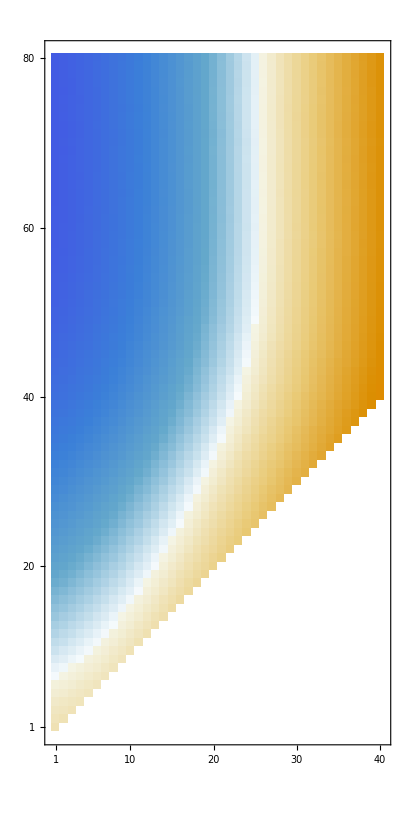

```mathematica
MatrixPlot[Transpose[g], DataReversed->{True,False}]
```